```mathematica
(*Mathematica*)
```

```mathematica
Clear[t,ta,tq,a,Q]
```

```mathematica
(*Simplex 5d Hypertetrahedron*)
```

```mathematica
t={{1,0,0,0,1},
{-1/2,Sqrt[3]/2,0,0,1},
{-1/2,-Sqrt[3]/2,0,0,1},
{0,0,1,0,1},
{0,0,0,1,1}}
```

{{1,0,0,0,1},{-1/2,(√3)/2,0,0,1},{-1/2,-(√3)/2,0,0,1},{0,0,1,0,1},{0,0,0,1,1}}

```mathematica
N[Det[t]/12]
```

0.216506

```mathematica
ta={{a,0,0,0,1},
{-a/2,a*Sqrt[3]/2,0,0,1},
{-a/2,-a*Sqrt[3]/2,0,0,1},
{0,0,a,0,1},
{0,0,0,a,1}}
```

{{a,0,0,0,1},{-a/2,(√3 a)/2,0,0,1},{-a/2,-(√3 a)/2,0,0,1},{0,0,a,0,1},{0,0,0,a,1}}

```mathematica
Solve[Det[ta]/12==1/6,a]
```

{{a→-(√2)/3^(3/8)},{a→-(ⅈ √2)/3^(3/8)},{a→(ⅈ √2)/3^(3/8)},{a→(√2)/3^(3/8)}}

```mathematica
a=(√2)/3^(3/8)
```

```mathematica
N[(√2)/3^(3/8)]
```

0.936687

```mathematica
(* Hyperbolic 3 Manifold edge scaling by a=(√2)/3^(3/8)*)
```

```mathematica
tq={{Q*a,0,0,0,1},
{-Q*a/2,Q*a*Sqrt[3]/2,0,0,1},
{-Q*a/2,-Q*a*Sqrt[3]/2,0,0,1},
{0,0,Q*a,0,1},
{0,0,0,Q*a,1}}
```

{{(√2 Q)/3^(3/8),0,0,0,1},{-Q/(√2 3^(3/8)),(3^(1/8) Q)/(√2),0,0,1},{-Q/(√2 3^(3/8)),-(3^(1/8) Q)/(√2),0,0,1},{0,0,(√2 Q)/3^(3/8),0,1},{0,0,0,(√2 Q)/3^(3/8),1}}

```mathematica
(*mass=volume*)
```

```mathematica
Det[tq]/12
```

Q^4/6

```mathematica
(*constants:cgs units*)
```

```mathematica
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=125.38*10^3*me/mev;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
α=1/137.035999206;
```

```mathematica
(* graviton at spin 2?!*)
```

```mathematica
(*hypertetrahedron simplex particle in 5d: boson*)
```

```mathematica
mg=Q^4/6/.Q->G
```

```mathematica
(*fundamental alpha quantum*)
```

```mathematica
α*me/mg
```

2.012

```mathematica
(*quantum mass = quantum volume*)
```

```mathematica
qg=Q/.Solve[Q^4/6==(2*Pi*hbar/(Q*c)),Q]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{-5.40101×10^-8-3.92406×10^-8 ⅈ,-5.40101×10^-8+3.92406×10^-8 ⅈ,2.063×10^-8-6.34927×10^-8 ⅈ,2.063×10^-8+6.34927×10^-8 ⅈ,6.67602×10^-8}

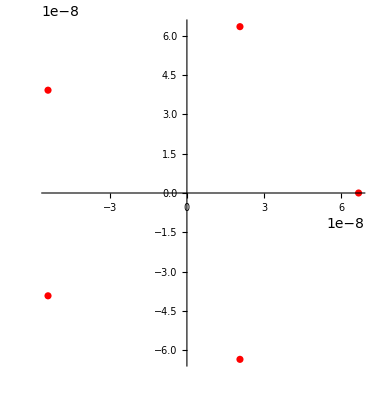

```mathematica
ComplexListPlot[qg,PlotStyle->Red]
```

```mathematica
(*gravitational charge*)
```

```mathematica
qg/G
```

{-0.809432-0.588087 ⅈ,-0.809432+0.588087 ⅈ,0.309176-0.951545 ⅈ,0.309176+0.951545 ⅈ,1.00051}

```mathematica
(*Weyl gauge*)
```

```mathematica
qg/(hbar*c/e)
```

{-0.820558-0.59617 ⅈ,-0.820558+0.59617 ⅈ,0.313425-0.964623 ⅈ,0.313425+0.964623 ⅈ,1.01427}

```mathematica
(*Higgs Boson as hyperbolic 3 manifold tetrahedron*)
```

```mathematica
mh=(3/4)*G^3
```

2.22815×10^-22

```mathematica
mh/mhiggs
```

0.99689

```mathematica
(*Weinberg weak angle as gravitational*)
```

```mathematica
mg/mh/G
```

0.222222

```mathematica
%/θw0
```

0.961136

```mathematica
(*sea saw of massive bosons: E_8 A_5 Dodecahedron 30 Fuchsian edge group particle*)
```

```mathematica
Sqrt[mh*mg]
```

2.71322×10^-26

```mathematica
Sqrt[mh*mg]/me
```

```mathematica
(*.10Higgs boson as five complex particles*)
```

```mathematica
(3/4)*qg^3
```

{6.89598×10^-23-2.12236×10^-22 ⅈ,6.89598×10^-23+2.12236×10^-22 ⅈ,-1.80539×10^-22+1.31169×10^-22 ⅈ,-1.80539×10^-22-1.31169×10^-22 ⅈ,2.23158×10^-22}

```mathematica
(*end*)
```